1. The densities

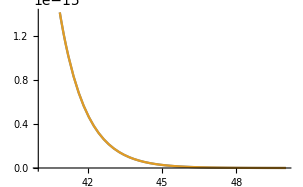
1.1 Exact density :
The well know wave function of hydrogen atom: Ψ_nlm(r,θ,φ)=ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l -l+n-12 l+1(2 r)/n Y_l^m(θ,φ)                          (eq.1) 
here -l+n-12 l+1z   is a generalized Laguerre polynomial of degree n − ℓ − 1, Y_l^m(θ,φ) is a spherical harmonic function of degree ℓ and order m.
so the density n_ex(r)=4 π ∫_0^π ∫_0^(2 π) 2 sin(θ) ∑_(n=1)^g ∑_(l=0)^(n-1) ∑_(m=-l)^l Abs[Ψ_nlm(r,θ,φ)]^2 ⅆφⅆθ, and it’s also ok to use ρ(r)=8∑_(n=1) 1/n^4 ⅇ^(-(2 r)/n) (n (n-21(2 r)/n)^2+((2 r)/n-2 n) n-11(2 r)/n n-21(2 r)/n+n (n-11(2 r)/n)^2)  [1]
-Graphics-
fig[1]: the two kinds of expressions of the exact density for 10 electrons.
 
 
 To calculate the total number of electrons, define  (ñ)_ex(r)=r^2 n_ex(r). Here the g is the number of the layers. 
 For example if there are 10 electrons: n_(ex 10)(r)=4 π ∫_0^π ∫_0^(2 π) 2 sin(θ) ∑_(n=1)^3 ∑_(l=0)^(n-1) ∑_(m=-l)^l Abs[Ψ_nlm(r,θ,φ)]^2 ⅆφⅆθ, the number in the subscription is the number of the electrons.

1.2 Approximation - Thomas Fermi density :      

For atoms, the potential should be Coulomb potential. 
After rewriting in atomic units, for isotropic 3D version: 
n_TF(r)=(4 2/r+μ (√(2/r+μ))^3)/(3 π)                            (eq.2)
similarly, define  (ñ)_TF(r)=r^2 n_TF(r),  x here is a Heaviside step function.

Eg:n_(10 TF)(r)=(4  (√(2/r-0.164414))^3 2/r-0.164414)/(3 π)

1.3Approximation-n_(3')(r):       

After relating n(r) to unitary evolution operator U=e^(it/ħ H(P,R)), splitting the evolution into 3 steps and change the kinetic energy first[2],
we can obtain U_(3') =e^(-it/(4ħ m)P^2)e^(-it/ħ V(R))e^(-it/(4ħ m)P^2) and an approximation: 
n_(3')(r) = 2∫da ((k_(3'))/(2 π a))^D D2 a k_(3')                                   (eq.3)
with
   k_(3')=(√(2m(μ-V(a+r))) μ-V(a+r))/ħ is the Fermi wave number, D is the the dimension.
For atoms, the potential should be Coulomb potential. By using atomic units, and for example, if we are considering the isotropic 3D version, we can transmit this definition into:
n_(3')(r)=∫_G 1/(2 π a)2 sinθ (2/(√(a^2-2 a r cos θ+r^2))+μ)^(3/2) 32 a √(μ+2/(√(a^2-2 r a cos θ +r^2)))da dθ                         (eq.4)
G is an implicitRegion:(-2/μ)^2>a^2-2 a r cos θ+r^2 and a≥0,0≤θ≤π. Define (ñ)_(3')(r)=r^2 n_(3')(r), and an example:
n_(3'10)(r)=∫_G 1/(2 π a)2 sin θ (2/(√(a^2-2 a r cos θ+r^2))-0.164414)^(3/2) 32 a √(-0.164414+2/(√(a^2-2 a r cos θ+r^2)))

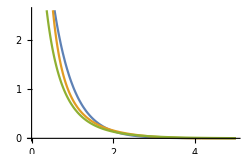
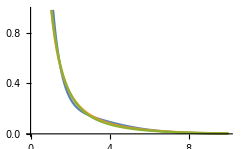
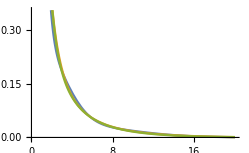
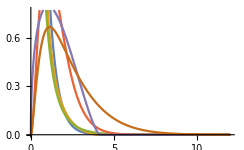
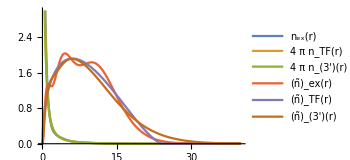
-Graphics-
                                      (2.a)-Graphics-
                                       (2.b)
-Graphics-
                                     (2.c)-Graphics- 
                                      (2.d) 

                                                       (2.e)
-Graphics-
                                                              (2.f)

fig[2] : (2.a), (2.b), (2.c) show n_ex, n_TF, and n_(3'), for 1, 2, 3 full Bohr shells of electrons, that equal to the situations of 2, 10, 28 electrons .
(2.d), (2.e), (2.f)  show the (ñ)_ex, (ñ)_TF, and (ñ)_(3') for 1, 2, 3 shells.


1.4 Approximation- n_7(r)|_(ϵ→0)

Similarly, n_7(r)|_(ϵ→0) can be obtained by splitting the evolution, but it is helped by Airy averaging and much more complicated, at the expense of better accuracy.
n_7(r)|_(ϵ→0)=2 ∫xⅆx∫(k_7^(x)/(2 π a))^D D2 a k_7^(x)ⅆa                                                 (eq.5)
k_7^(x)=((1/ћ[2m(μ-1/3 V(r)-2/3 V(r+a))-(x((1/3[∇V(r+a)])^2))^(1/3)])_+)^(1/2)
=1/ћ 2m(μ-1/3 V(r)-2/3 V(r+a))-(x((1/3[∇V(r+a)])^2))^(1/3)√(2m(μ-1/3 V(r)-2/3 V(r+a))-(x((1/3[∇V(r+a)])^2))^(1/3))                                 (eq.6)        
And consider that the potential for an hydrogen atom is Coulomb potential and write this expression in atomic units,
for isotropic 3D, it is
∫_G 1/(2 π a^2)(√(μ+2/(3r)+4/(3 √(r^2+a^2+2 r a Cos θ))-(x(1/(3(r^2+a^2+2 r a Cos θ)^2)))^(1/3)))^3
32 a √(μ+2/(3r)+4/(3 √(r^2+a^2+2 r a Cos θ))-(x(1/(3(r^2+a^2+2 r a Cos θ)^2)))^(1/3))x Sinθⅆxⅆθⅆa                     (eq.7)                    
the G here is the region satisfies (μ-1/3 V(r)-2/3 V(r+a))-(x((1/3[∇V(r+a)])^2))^(1/3)≥0
And similarly we can also define a (ñ)_7(r)|_(ϵ→0).

2. Numerical works and cutoffs of potential for n_(3')(r)

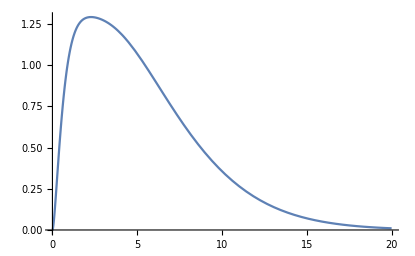
Thought it's not so difficult to calculate the values of n_(3'), we still need a simpler form for it so that we can make a faster  evaluation  as well as  a clear hint for analysis. Before we discuss n_(3')and n_TF,we can obtain a formula by changing variable from a to x=a +r:

n_(3')(r)=∫_0^(-2/μ) x/(2 π r)(μ x+2)^2 (3-((r-x)^2 (μ x+2))/x-3-((r+x)^2 (μ x+2))/x)ⅆx                                                                              (formula.1)

As for how to obtain this formula please see steps in (3.2.3). It's a integral of only one variable x.It will be much faster if we use such a formula, or a summation instead of the integral.  However if we want a finite value and when input x=0,and the computer may not evaluate it. Then we need a cutoff on coulomb potential and plug specific chemical potential into this expression and use summation instead of integral. When the the step length is small enough, we can use such a  summation instead of integral. 
-Graphics- 
          fig[3]: the graph shows (ñ)_(3') by evaluate a summation form in formula.1

By the way, we can also know what are different behaviors of n_(3')  and n_TF by choosing different cutoffs.

2.1Different cutoffs on coulomb potential
 
By simple analyses and some plots, we know that if the cutoff is very large (eg, 0.25 Bohr radius), the value of n_TF at r=0 will be closer to the exact value than n_(3') ;if the cutoff is very small(eg, 0.0005 Bohr radius), the n_(3') may be "better" than n_TF.

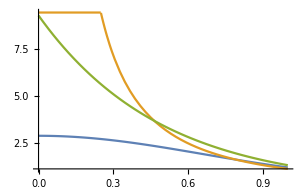
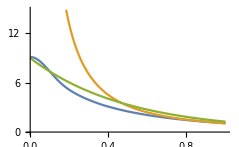
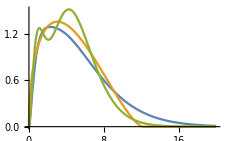
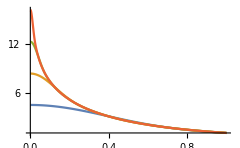
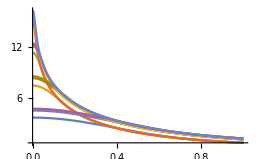
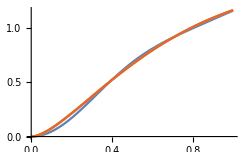
-Graphics-    -Graphics- 
                                     (4.a)                                                                                                                 (4.b)
                                                                                                                                                                                                    -Graphics-        -Graphics-                     
                          (4.c)                                                                                                                                              (4.d)
-Graphics-                      -Graphics-
                         (4.e)                                                                                                                                                       (4.f)

fig[4]  (4.a)is  about n_(3') for 28 electrons with a cutoff at 0.25 a_0; (4.b)is  about n_(3') for10 electrons with a cutoff at 0.0005 a_0; 
 in (4.c) , the(ñ)_(3')(r) is obtained by a summation form of formula.1, we can see that summation is good enough.; in(4.d) form bottom to the top, the four lines show the n_(3'(10))(r) with cutoff: 0.5, 0.05, 0.005 and 0.0005; (4.e) and (4.f)show how the n_(3')  and  (ñ)_(3') with different cutoffs for 2,10, 28 electrons.

We can see that the difference between each two adjacent lines become smaller  and smaller with the decrease of the cutoff, and when it goes to about 0.0005~0.00005, the influence of this difference will become quit small when we calculate the total particle number. And if we assume the cutoff is caused by the nucleus, the radius of nucleus is a bout 10^-15 m, or say  10^-4~10^-5 Bohr radius. After considering both the accuracy and the speed,0.0005~0.00005 is a good range to select the cutoff.

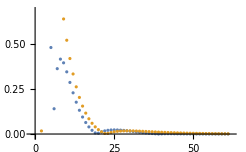
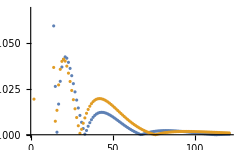
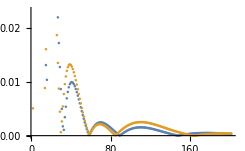
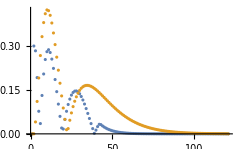
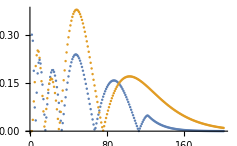
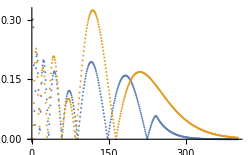
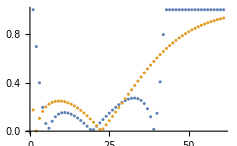
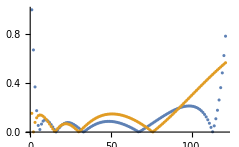
2.2compare n_TF and n_(3') by sample points 

Choosen Cutoff:0.0005  Sample steplength:0.1
Define some quantities to show the errors:
define the absolute errors by the absolute value of the differences between appoximations and exact densiy：
 (d_(3'))_(N)=|n_(3'(N))-n_(ex(N))|        ((d̃)_(3'))_(N)=|(ñ)_(3'(N))-(ñ)_(ex(N))|                                    (eq.8)
d_TF_(N)=|n_(TF(N))-n_(ex(N))|      ((d̃)_TF)_(N)=|(ñ)_(TF(N))-(ñ)_(ex(N))|                                     ( eq.9)
define the relative errors by the ratios of absolute errors and the sum:	
R_(3'(N))=Abs[n_(3^`(N))-n_(ex(N))]/(n_(3'(N))+n_(ex(N)))      (R̃)_(3'(N))=Abs[n_(3^`(N))-n_(ex(N))]/((ñ)_(3'(N))+(ñ)_(ex(N)))                             (eq.10)
                  R_(TF(N))=Abs[n_(3^`(N))-n_(ex(N))]/(n_(TF(N))+n_(ex(N)))     (R̃)_(TF(N))=Abs[n_(3^`(N))-n_(ex(N))]/((ñ)_(TF(N))+(ñ)_(ex(N)))                             (eq.11)
the N in subscription is the number of the electrons
 
-Graphics-  -Graphics-
                                        (5.a)                                                                                                           (5.b)
-Graphics--Graphics- 
                                             (5.c)                                                                                                   (5.d)
-Graphics--Graphics-
                                    (5.e)                                                                                                      (5.f)
                                                                                                               
-Graphics--Graphics-
                               (5.g)                                                                                                           (5.h)
-Graphics--Graphics-
                                 (5.i)                                                                                                             (5.j)
-Graphics--Graphics-
                                             (5.k)                                                                                                  (5.l)
fg[5]the group of garphs above,  in each graph,use blue points for n_TF, orange points for n_(3').:
(5.a),(5.b),(5.c),show d_TF_(2)and (d_(3'))_(2), d_TF_(10)and (d_(3'))_(10), d_TF_(28)and (d_(3'))_(28);
      (5.d), (5.e), (5.f)show((d̃)_(3'))_(2) and ((d̃)_TF)_(2),  ((d̃)_(3'))_(10) and ((d̃)_TF)_(10) , ((d̃)_(3'))_(28) and ((d̃)_TF)_(28) ;
      (5.g), (5.h), (5.i) show R_(3'(2)) and R_(TF(2)), R_(3'(10)) and R_(TF(10)), R_(3'(28)) and R_(TF(28));
      (5.j), (5.k), (5.l) show OverTilde[(R̃)_(3'(2)) and (R̃)_(TF(2)), R]_(3'(10))and (R̃)_(TF(10)), (R̃)_(3'(28)) and (R̃)_(TF(28)).

By some plots and anlysing the errors  now we know that n_(3')is even not better than n_TF, but for the situation when r is very samll or very large，it seems that the properties of n_(3') is better than n_TF as the n_(3')won't be 0 when r is large, and it diverge slower than n_TF when r is small. Then we will disscuss the limiting behaviors of the densities.

3. Limiting behavior of the densities

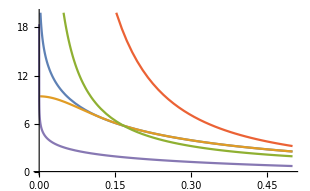
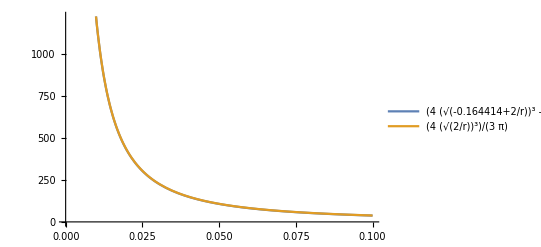
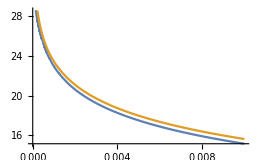
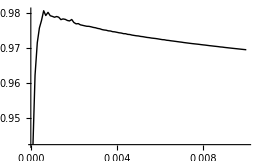
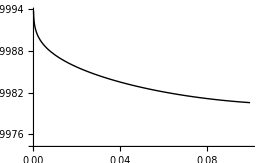
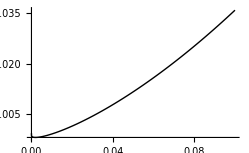
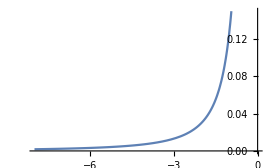
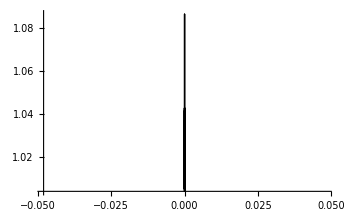
By doing numerical works we found the densities may be infinity at r=0 and n_(3') diverges slower than 1/r and much slower than n_TF that we can see in fig[6]. If we really want to use those approximations for a hydrogen atom, it’s necessary to know the limiting behaviors because we need to know if those approximations is really better than n_TF when r is small or large, and we should also make sure that we can obtain a useful finite value when we evaluate the total number of the particles by such a density. 
-Graphics-
 fig[6] There are different divergencies: the red line is r^(-3/2), green line is 1/r, blue line is n_(3') with 10 electrons,
  orange line is for formula.1 with a cutoff, the purple line is -log_er
 
 3.1  limiting behavior for densities when r is small

3.1.1 behavior of  n_TF
 
 As we have an expression for n_TF:     
 n_TF(r)=1/(3 π)4 2/r+μ (√(2/r+μ))^3                              (eq.12)                      
 It is easy to show that when r approaches 0,because 2/r will become so large that the chemical potential μ can just be ignored, hence that   n_TF→1/(3 π)4 (√(2/r))^3 when r→0.
   
   -Graphics-
  Fig[7]   The graph shows n_(TF(10))and(4 (√(2/r))^3)/(3 π). We can hardly distinguish them. 

  It’s a large divergency but it will still converge when we apply r^2 to calculate the total number of electrons.
 
 3.1.2 behavior of  n_(3')
   	
   	Before the strict discussion, we know it must diverge slower than  1/r. And a hint: if we choose different factors for a logarithm, some times it will diverge faster than n_(3') and some times it will diverge slower than n_(3'). That numerical hint suggests us that the n_(3') should have the logarithm-like divergency and we need to find a proper factor. As a start I tried  to compare it with a logarithm by choosing -32/(3 π) as the factor.
   	  

   -Graphics-  -Graphics-
                           (8.a)                                                               (8.b)
   Fig[8] blue line in (8.a) is the n_(3'(10)) , the orange line is (32 log_ⅇ(1/r))/(3 π), the line in (8.b) is the ration(3 π n_(3'))/(32 log_ⅇ(1/r)). 
   Both (8.a) and (8.b) are for isotropic 3D version
   
The ratio will keep around 1 when r is small, but if r decrease, the ratio will continue to decrease. What is the truth?

Now we need to discuss about the asymptotic by its analytic expression. Since we have the original definition n_(3')(r) = 2∫(da((k_(3')(r+a))/(2 π a)))^3 32 a k_(3')(r+a) ,  let r=0 and use Dirac function to change the variable, we can obtain
   n_(3')(0) = 2∫(da((k_(3')(a))/(2 π a)))^3 32 a k_(3')(a)~∫(da(1/a))^4 δ(y-2 a k_(3')(a))∫(dy(y))^3 3y                (eq.14)
   by properties of Dirac function and Meijer-G function [3,5], the result of the integral above is:
   n_(3')(0)= -1/π16 (-4 G_(1,3)^(2,0)(1/4 y^2|1
0,0,-3)-1/y μ^2 (-y+y 2y+2 1y)+(5 μ (y^2-8 2y))/(2 y^2))                      (eq.15)

 And n_(3')(0) should be a specific "value”, the integral of y is a definite integral, though y can start from -∞ to +∞, when y take a negative value or other values out of the domain of  2 a k_(3')(a), we can not find root for the expression in delta function, then it will be zero. So we should just make a difference between n_(3'|y→0)(0) and n_(3'|_(y→m))(0), here the m is the maximum of 2ak_(3'). We know that when y=0, n_(3')(0) will be infinity, otherwise it will be a finite value, which means n_(3'|_(y→m))(0) does not play a role  when we compare it with infinity. So we only need to analyse  n_(3')(0) when y→0. If we just let n_(3')(0) be divided by log(1/y), it will be zero at y=0, but there is a question: shall we compare it with log(1/y)? Or what is the correlation between y and r or a? As we use y-2 a k_(3')(a) in Dirac delta function, I compared n_(3')(0) with log((2 μ)/(√(μ y^2+4)-2))  , here(√(μ y^2+4)-2)/(2 μ)is a root of equation  y-2 a k_(3')(a)=0, and plug y=2 a k_(3')(a) into n_(3')(0), then compare it with log(1/a)
 

   -Graphics-      -Graphics-             
                                             (9.a)                                                                                                      (9.b)      
   fig[8 ]: line in (a) is the ratio: n_(3')(0) divided by 16/(3 π)log((2 μ)/(√(μ y^2+4)-2)), the variable is y;
    (b) is about the ratio: n_(3')(0)(plug y=2 a k_(3')(a) into it) divided by16/(3 π)log(1/a), the variable is a.                  


 [y0((-24 (-4 G_(1,3)^(2,0)(y^2/4|1
0,0,-3)-(5μ (-8 2y))/(2 y^2)-(μ^2 (+2 1y+y 2y))/y))/(16 log_ⅇ((2 μ)/(√(4-μ y^2)-2))))]=1                   （eq.16）,
  the answer should be 16/(3 π)log(1/r)

Maybe it is still a little farfetched.  And we can also start from another angle. 
Since we got the formula:
 n_(3')(r)=∫_0^(-2/μ) x/(2 π r)(μ x+2)^2 (3-((r-x)^2 (μ x+2))/x-3-((r+x)^2 (μ x+2))/x)ⅆx 
 we can start from that formula and expand its integrand
3-(2/x+μ) (x-r)^2=∑_(n=0)^∞ ((-1)^n (x-r)^(2 n) (μ+2/x)^n)/((3)_n n!)                 (eq,17)
 3-(2/x+μ) (x+r)^2=∑_(n=0)^∞ ((-1)^n (x+r)^(2 n) (μ+2/x)^n)/((3)_n n!)                          (eq.18)

make difference of   (eq,17)and  (eq.18)
3-(2/x+μ) (x-r)^2-3-(2/x+μ) (x+r)^2
(=∑)_(n=0)^∞1/((3)_n n!)(-1)^n( (x-r)^(2 n)-(x+r)^(2 n)) (μ+2/x)^n                              (eq.19)

continue to do binomial expansions for (x-r)^(2n)-(x+r)^(2n) and (μ+2/x)^(n+2):
 (x-r)^(2 n)-(x+r)^(2 n)=∑_(z=1)^n (-2) Binomial[2n, 2z-1]r^(2 z-1) x^(2 n-2 z+1)           (eq.20) 
 (μ+2/x)^(n+2)=∑_(f=0)^(n+2) 2^f  Binomial[n+2, f](1/x)^f μ^(-f+n+2)                                   (eq.21)   

the integral becomes:

∫_0^(-2/μ) x/(2 π r)∑_(n=0)^∞ 1/((3)_n n!)(-1)^n∑_(z=1)^n (-2) Binomial[2n, 2z-1]r^(2z-1) x^(2 n-2 z+1) ∑_(f=0)^(n+2) 2^f  Binomial[n+2, f](1/x)^f μ^(-f+n+2)ⅆx
=1/(2 π)∫_0^(-2/μ) ∑_(n=0)^∞ ∑_(z=1)^n ∑_(f=0)^(n+2) Θ_(n,z,f)G_(n,f,z) ⅆx                                           (eq.22)
      
    the factors: Θ_(n,z,f)=((-1)^(n+1)2^(f+1))/((3)_n n!) Binomial[2n, 2z-1] Binomial[n+2, f]μ^(-f+n+2)       
the power terms: G_(n,f,z)=r^(2 z-2) x^(2 n-2 z+2-f) 

let's depose the integral into two parts:
I_1=1/(2 π)∫_r^(-2/μ) ∑_(n=0)^∞ ∑_(z=1)^n ∑_(f=0)^(n+2) Θ_(n,z,f)G_(n,f,z) ⅆx                                   (eq.23.a)
I_2=1/(2 π)∫_0^r ∑_(n=0)^∞ ∑_(z=1)^n ∑_(f=0)^(n+2) Θ_(n,z,f)G_(n,f,z) ⅆx                                        (eq.23.b)
1/(2 π)∫_0^(-2/μ) ∑_(n=0)^∞ ∑_(z=1)^n ∑_(f=0)^(n+2) Θ_(n,z,f)G_(n,f,z) ⅆx=I_1+I_2=n_(3')(r)       (eq.23.c)

now calculate the integral I_1 and assume r is very small, we can just take care of the power terms,the integral of  G_(n,f,z) could give 2 kinds of results:

r^(2 z-2) ((-2/μ)^(-f+2 n-2 z+3)-r^(-f+2 n-2 z+3))(-f+2 n-2 (z+3))^-1      when order of G_(n,f,z) is not -1

r^(2 z-2) (log_ⅇ(-2/μ)-log_ⅇ(r))                                                       when order of G_(n,f,z) is -1

As for r^(2 z-2) ((-2/μ)^(-f+2 n-2 z+3)-r^(-f+2 n-2 z+3))(-f+2 n-2z+3)^-1, no mater what the original order is, the orders of r in this expression are -f+2 n-2 z+3+2 z-2=1+f+2 n and 2z-2, both of them are nonnegative, the contributions of that kind of terms will be 0 or constants, and the r is very small hence that they play no role. Only the logarithm terms can make contributions. If we want to get that one, z,  f and n must satisfy: 2z-2=0, 2n-2z-f+2=-1. So we get only one term with z=n=1 and f=3. If we want to know what’s the constant term, just look back to
r^(2 z-2) ((-2/μ)^(-f+2 n-2 z+3)-r^(-f+2 n-2 z+3))(-f+2 n-2z+3)^-1
=(r^(2 z-2) 2^(-f+2 n-2 z+3) (-1/μ)^(-f+2 n-2 z+3))/(-f+2 n-2 z+3)-r^(-f+2 n+1)/(-f+2 n-2 z+3)                                             (eq.24)
 the second term will be zero unless z=1 or 1-f+2 n=0, but that is the term 1/x,with z=1, n=1, f=3. 
so we can only assume z=1, and use summation:
 C= ∑_(n,f) (2^(2 n+3) μ^(1-n) (-1)^(-f+3 n+2))/(π f! (n-1)! (-f+2 n+1) (-f+n+2)!)                                   (eq.25)
 except the term with  n=1 meanwhile  f=3.
-Graphics-
fig[10]: the line show the constant C.


That summation will converge to a finite value with the increasing n and f.

For example,  C=11.7269695821 when chemical potential μ=-0.164414
Now check the factor of 1/x:

-1/(2 π)Θ_(n,z,f)=-1/(2 π)((-1)^(1+1)2^(3+1))/((3)_1 1!) Binomial[2, 1] Binomial[3, 3]μ^0=-16/(3 π),which agree with what we have by factor of MeijerG function by seting r=0
Because the domain of I_1 will approach zero,so I_1 vanishes. 


           
-Graphics-
                                                    (11.a)
            -Graphics-     
                                                            (11.b)                                                                                             
fig[11]: (11.a) is the ratio:(n_(3'))/(16/(3 π) log_ⅇ(1/r )); (11.b) is the ratio: (n_(3'))/(16/(3 π) log_ⅇ(1/r )+C) ; 
both (11.a) and (11.b) are for isotropic 3D version.


The density n_3.~-16/(3 π) log_ⅇ(r)+C, when r is aboμt 10^-3 a_0,the valμe of -16/(3 π) log_ⅇ(r)is very close to the constant C,that's why the density looks like -32/(3 π)log_ⅇ(r)in fig[7]. 
However, if we continue to decrease r to a extremely small value, and the constant won’t play a role again, then I_1+I_2+C~-16/(3 π)log_ⅇ(r), so in fig[7] the density looks more likely to be -16/(3 π)log_ⅇ(r). For 1-D: the factor of logarithm is 2/π; for 2-D, it’s 4/π.
-Graphics-
fig[12] shows the ration between 2/π log_e 1/r and 1D version of n_(3')
 
 3.1.3 behavior of  n_7(r)|_(ϵ→0)   
 
 The definition:
  n_7(r)|_(ϵ→0)=2 ∫xⅆx∫(k_7^(x)/(2 π a))^D D2 a k_7^(x)ⅆa
For isotropic 3D, it is
∫xⅆx∫1/(2 π a^2)( √(μ+2/(3r)+4/(3 √(r^2+a^2+2 r a Cos θ))-(x(1/(3(r^2+a^2+2 r a Cos θ)^2)))^(1/3)))^D 32 a √(μ+2/(3r)+4/(3 √(r^2+a^2+2 r a Cos θ))-(x(1/(3(r^2+a^2+2 r a Cos θ)^2)))^(1/3))sin θⅆθⅆa

It’s difficult to get the numerical hint as before because not only the expression but also the codes are so complicated. We should start from this expression, first we can integrate over the angel θ:

Assume vector r’=r+a, a=√(r'^2+r^2-2r r'cos θ'), the expression above become:

n_7(r)|_(ϵ→0)=2∫xⅆx∫((√(μ+2/(3r)+4/(3r')-(x(1/(3 r'^4)))^(1/3)))/(2 π √(r'^2+r^2-2r r'cos θ')))^3
32 √(r'^2+r^2-2r r'cos θ') √(μ+2/(3r)+4/(3r')-(x(1/(3 r'^4)))^(1/3))r'^2 Sinθ'ⅆθ'ⅆr'ⅆφ'                               (eq.26)
sin θ’ⅆ θ’= - ⅆ cos θ’, set t=cos θ’, the integral of angle become:

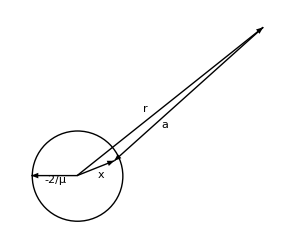
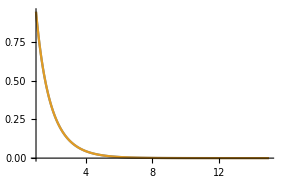
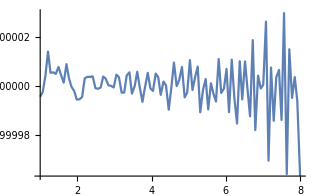
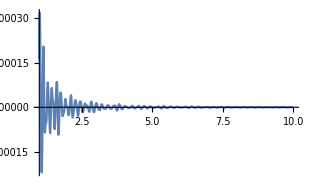
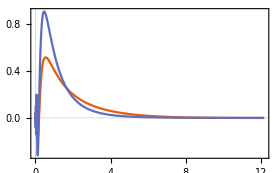
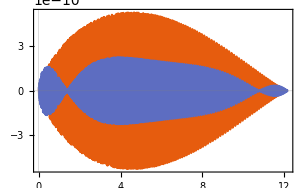
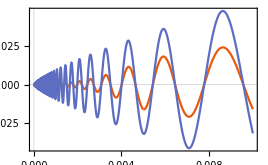
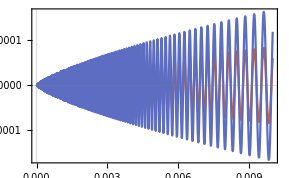
∫_-1^1 ((r'^2 (√(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')))^D 32 √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')) √(r^2-2 t r' r+r'^2))/(2 π^2 (√(r^2-2 r t r'+r'^2))^3))ⅆt,
Look at 2a k_7^(x), we can rewrite it as b √(1-c t) by set b=2 k_7^(x)√(r^2+r'^2), c= (2 r r')/(r^2+r'^2) the integral become
 ((r'^2(√(μ-(x(1/(3 r'^4)))^(1/3)+4/(3 r')+2/(3 r))))^3)/(2 π^2(√(r^2+r'^2))^3)∫_-1^1 (3b √(1-c t))/(√(1-c t))^3 ⅆt,
because  J_α(z)=(z/2)^α/(Γ(α+1))α+1-z^2/4                               
 so we can write

 (3b √(1-c t))/(√(1-c t))^3=b^3/(8Γ(4)) 4-b^2/4(1-c t)                                   (eq.27)
d/dt β-z^2/4=1/β β+1-z^2/4(dz/dt)

Assume G(t)=g  3-b^2/4(1-c t), 
(dG(t))/(d t)= (g b^2)/12 4-b^2/4(1-c t)=b^3/(8Γ(4)) 4-b^2/4(1-c t),
 so the factor g=b/(4c)=k_7^(x)/(4r r')(r^2+r'^2)^(3/2) ,  the result of the integral of angle is
  ((r'^2(√(μ-(x(1/(3 r'^4)))^(1/3)+4/(3 r')+2/(3 r))))^3)/(2 π^2(√(r^2+r'^2))^3)k_7^(x)/(4r r')(r^2+r'^2)^(3/2)(3-b^2/4(1-c t)-3-b^2/4(1+c t))
 =((k_7^(x))^4 r')/(8 π^2 r)(3-(k_7^(x))^2(r-r')^2-3-(k_7^(x))^2(r+r')^2)
 =((k_7^(x))^4 r')/(4 π^2 r)((22 k_7^(x)(r-r'))/((k_7^(x)(r-r'))^2)-(22 k_7^(x)(r+r'))/((k_7^(x)(r+r'))^2))
 =((k_7^(x))^2 r')/(4 π^2 r)((22 k_7^(x)(r-r'))/(r-r')^2-(22 k_7^(x)(r+r'))/(r+r')^2)                                  (eq.28)        
 So we can rewrite the density as 
 1/(4 π^2)∫xⅆx∫(k_7^(x))^2 r'((22 k_7^(x)(r-r'))/(r-r')^2-(22 k_7^(x)(r+r'))/(r+r')^2)ⅆr'
 =1/(4 π^2)∫xⅆx∫((-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')r')r')/r(1/(r-r')^2 22 (r-r')√(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')) -(1/(r+r')^2 22 √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r'))(r+r') ))ⅆr'       (formula.2)
or like ((k_7^(x))^4 r')/(8 π^2 r)(3-(k_7^(x))^2(r-r')^2-3-(k_7^(x))^2(r+r')^2), 
and this is also a way to obtain the (formula.1). The first Bessel function in the integrand is for r’ is along r, the second one is for r’ along -r.  
Now, if  we start at formula.2, it is possible to  avoid a discussion: where does the singularity come from? The situation of a = -r and r’ comes to 0, or r’ come close to r? Because in formula.2, when r’ is much smaller than r and a, r-r’ will be the same as r+r’, then the difference of two Bessel function will be 0. So in this case we can split the integral into 2 piece like what we did for n_(3')(r), I_1is from 0 to r, I_2 is from r to somewhere. When r approach 0, I_1will just vanish and we can obtain an expression of r from I_2.
But there is still a variable x which has no physical meaning here, it’s better to integrate it over if we want to analyse the limiting behavior.
let’s think about an integral of x with the integrand 
J_D(2 a k_7^(x))((k_7^(x))^D)/a^D Ai(x)=J_D(2 a k_7^(x))((a k_7^(x))^D)/a^(2D)Ai(x)=J_D(2 a √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')))((a √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')))^D)/a^(2D)Ai(x)          (eq.29)
If we use A=a^2(μ+2/(3 r)+4/(3 r')), B=(a^2(1/(3 r'^4)))^(1/3), then we can rewrite the integrand into J_D(2 √(A-B x))( √(A-B x))^D/a^(2D)Ai(x). 
Though it looks like a simple expression, it will be difficult to integrate over x directly. We can choose y=A-B x, then x=(A-y)/B, dx =-1/B dy. As the Heaviside step function requires, the y is from 0 to ∞. So now we should evaluate an integral 
-1/B∫_0^∞ (y^(D/2) D2 √y)/a^(2D)Ai((A-y)/B)ⅆy
As Airy function can be written in an integral representation[4]:
Ai(z)=1/π∫_0^∞ cos(τ^3/3+τ z)ⅆτ=Re(1/(2π)∫_(-∞)^∞ e^(i(τ^3/3+τ z))ⅆτ), 
as there’s no singularity on the complex plane for its integrand, we can also choose other contours that start at -∞ and end at instead of the real axis, which we can see later. As finally we need an real expression, we just use this integral expression in the integral and take out the real part of the result. 
So let’s evaluate-1/B∫_0^∞ (y^(D/2) D2 √y)/a^(2D)Ai((A-y)/B)ⅆy:
-1/B∫_0^∞ (y^(D/2) D2 √y)/a^(2D)Ai((A-y)/B)ⅆy
=Re[-1/(2π B)∫_(-∞)^∞ ⅆτ∫_0^∞ e^(i(τ^3/3+τ ((A-y)/B)))(y^(D/2) D2 √y)/a^(2D)ⅆτ]
=Re[-1/(2π B a^(2D))∫_(-∞)^∞ e^(i(τ^3/3+τ A/B))ⅆτ∫_0^∞ e^((-i y τ)/B) y^(D/2) D2 √yⅆy]                     (eq.30)
Integrate the variable y first:
now it’s better to use a formula [5,7]
 ∫_0^∞ z^(u-1/2)e^-αz J_(2v)(2β √z)ⅆz=(Γ(u+v+1/2))/(βΓ(2v+1))e^(-β/(2α))α^-u M_(u,v)(β^2/α)                   (eq.31)
 M_(u,v)(z)=z^(v+1/2)e^(-z/2)M(v-u+1/2;2v+1;z)                                              (eq.32)
 here M_(u,v) and M are the Whittaker function and Kummer’s confluent hypergeometric function. 
 For our case, u=(D+1)/2,v=D/2, z=y, α=(i τ)/B,β=1, v-u+1/2=0.  
  As M(0;2v+1;z)=1, we can easily obtain the result 
 ∫_0^∞ e^((-i y τ)/B) y^(D/2) D2 √yⅆy=1/(τ^(D+1) i^(D+1))B^(D+1)e^((i B)/τ)                            (eq.33) 
 But notice that, it’s not always true for all the τ because we need to make sure the integrand will converge.  If we look at (eq.31), we need to choose a proper τ so that the real part of α is always positive. B is always positive, that means the imaginary part of τ should keep negative. Look back to the integral representation of Airy function, we can choose a contour C which starts at -∞, goes through the lower half plane then ends at ∞.
Now we have 
-1/(2π B a^(2D))∫_(-∞)^∞ e^(i(τ^3/3+τ A/B))ⅆτ∫_0^∞ e^((-i y τ)/B) y^(D/2) D2 √yⅆy
=-1/(2π B a^(2D))∫_C e^(i(τ^3/3+τ A/B))ⅆτ 1/(τ^(D+1) i^(D+1))B^(D+1)e^((i B)/τ)
=-B^D/(2π i^(D+1)  a^(2D))∫_C (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ                     (eq.34)
Then it’s time to evaluate integral∫_C (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ. We can choose another semicircle arc with large radius, or any other symmetrical contour about the imaginary axis in the upper half-plane to close this contour, we call it C_R. For this closed contour[6], there is an essential singularity 0 enclosed, ∫_C (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ+∫_C_R (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ=2πi Res(0), and in fact we only concern about the real part :
Re[∫_C (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ]=Re[2πi Res(0)-∫_C_R (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ]
Due to the symmetry of the contour we choose, for an even D the contribution to real part from ∫_C_R (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)ⅆτ will just be 0; but for an odd D, it will be problematic and may need other discussions. 


-Graphics-
Fig[13] shows the closed anti-clockwise contour composed by C and C_R

It seems that this does not work for the case D=3, which we really concerned, but in formula.2 we have written 3D version as an expression of J_2. So it’s also ok to discuss about it.
For (e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1) , 0 is the essential singularity, if we want to use residue theorem we need to find the factor for 1/τ when we obtain its Laurent series.
As e^(z/2(t-1/t))=∑_(m=-∞)^∞ t^m mz is the generating function of first kind of Bessel function, we can do the similar thing:
(e^(i(τ^3/3+τ A/B+B/τ)))/τ^(D+1)=(e^(i(τ A/B+B/τ))e^(i τ^3/3))/τ^(D+1)=(e^((2 √A)/2( (iτ √A)/B-B/(i τ √A)))e^(i τ^3/3))/τ^(D+1)
=((e^(i τ^3/3))/τ^(D+1)∑)_(m=-∞)^∞( (iτ √A)/B)^m m2 √A
=( (iτ √A)/B)^D((e^(i τ^3/3))/τ^(D+1)∑)_(m=-∞)^∞( (iτ √A)/B)^m D+m2 √A
=( (i √A)/B)^D((e^(i τ^3/3))/τ∑)_(m=-∞)^∞( (iτ √A)/B)^m D+m2 √A             (eq.35)
After that we can also expand e^(i τ^3/3) at τ=0 and obtain
( (i √A)/B)^D((e^(i τ^3/3))/τ∑)_(n=-∞)^∞( (iτ √A)/B)^m D+m2 √A
=1/τ( (i √A)/B)^D ((∑)_(m=-∞)^∞( (iτ √A)/B)^m D+m2 √A)∑_(n=0)^∞ (i^n (τ^3)^n)/(3^n(3n)!)         (eq.36)
To pick up the factor of 1/τ,  m should be equal to -3n. 
So the factor is ( (i √A)/B)^D ∑_(n=0)^∞ i^n/(3^n(3n)!)( B/(i √A))^(3n) D-3n2 √A      
Combine what we have, then for D=2, we can write
 -B^2/(2π i^3  a^4)∫_C (e^(i(τ^3/3+τ A/B+B/τ)))/τ^3=-B^2/(i^2  a^4)( (i √A)/B)^2 ∑_(n=0)^∞ i^n/(3^n(3n)!)( B/(i √A))^(3n) 2-3n2 √A
=A/a^4∑_(n=0)^∞ (-1)^(n+1)/(3^n(3n)!)( B/(√A))^(3n) 2-3n2 √A                                         (eq.37) 
The result is real and only involving the quantities with physical meanings such as r.
Now recall formula.2,
 n_7(r)|_(ϵ→0)=1/(4 π^2)∫xⅆx∫((-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r')r')/(4 π^2 r))((22 √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r'))(r-r') )/(r-r')^2-(22 √(-(x(1/(3 r'^4)))^(1/3)+μ+2/(3 r)+4/(3 r'))(r+r') )/(r+r')^2)ⅆr'       (eq.38),
 
and similarly we can write a_1=r-r',a_2=r+r', then define A_1=a_1^2(μ+2/(3 r)+4/(3 r')),B_1=(a_1^2(1/(3 r'^4)))^(1/3), A_2=a_2^2(μ+2/(3 r)+4/(3 r')),B_2=(a_2^2(1/(3 r'^4)))^(1/3). 
Hence that we can rewrite formula.2 as
n_7(r)|_(ϵ→0)=1/(4 π^2)∫xⅆx∫r'/r(1/a_1^2(A_1-B_1 x)22 √(A_1-B_1 x) -1/a_2^2(A_2-B_2 x)22 √(A_2-B_2 x) )ⅆr'
=1/(4 π^2)(∫r'/r ⅆr'∫x 1/a_1^2(A_1-B_1 x)22 √(A_1-B_1 x) ⅆx)-1/(4 π^2)(∫r'/r ⅆr'∫x 1/a_2^2(A_2-B_2 x)22 √(A_2-B_2 x) ⅆx)            (eq.39)      
Both the two parts can be solved by what we have discussed above,  
1/(4 π^2)∫r'/r∑_(n=0)^∞ (-1)^(n+1)/(3^n(3n)!)(A_1/a_1^4( B_1/(√A_1))^(3n) 2-3n2 √A_1-A_2/a_2^4( B_2/(√A_2))^(3n) 2-3n2 √A_2)ⅆr',
to analyse it, we can split each integral into two parts,
I_1=1/(4 π^2)∫_0^r (r'/r∑)_(n=0)^∞(-1)^(n+1)/(3^n(3n)!)(A_1/a_1^4( B_1/(√A_1))^(3n) 2-3n2 √A_1-A_2/a_2^4( B_2/(√A_2))^(3n) 2-3n2 √A_2)ⅆr'               (eq.40.a)
I_2=1/(4 π^2)∫_r^s (r'/r∑)_(n=0)^∞(-1)^(n+1)/(3^n(3n)!)(A_1/a_1^4( B_1/(√A_1))^(3n) 2-3n2 √A_1-A_2/a_2^4( B_2/(√A_2))^(3n) 2-3n2 √A_2)ⅆr'                (eq.40.b)
As r decrease, I_1 will just vanish. And for I_2, we don’t really need to worry about the question where the integral end as the mainly contribution comes from a small neighbour of small r, so now the things become easy: to evaluate the integrals for each term, change r’ into r, let r approach 0, then pick up the infinity contributions.
Notice that a Bessel function can be expanded as a series as αz=∑_(k=0)^∞ ((-1)^k (z/2)^(α+2 k))/(k! k+α+1)when α>0 and -αz=(-1)^α αz when α is an integer[8]. Define the total contribution as ∑_(n=0)^∞ ∑_(k=0)^∞ C_(n,k), C_(n,k) is the contribution of the term with n and k. And temporarily use a notation: ∫_r^s f(x)=-F(x)|_r=-F(r). 
Based on those preparations,  we start to evaluate the term with n=0, k=0:
∑_(k=0)^∞ C_(0,k)=-1/(4 π^2)∫_r r'/r(A_1/a_1^4 22 √A_1-A_2/a_2^4 22 √A_2)ⅆr'                             (eq.41)
C_(0,0)=-1/(4 π^2)∫_r r'/r(A_1/a_1^4 (√A_1)^2/3-A_2/a_2^4(√A_2)^2/3)ⅆr'
=-1/(8 π^2)∫_r r'/r(A_1^2/a_1^4  -A_2^2/a_2^4)ⅆr'
=-1/(8 π^2)∫_r r'/r((μ+2/(3 r)+4/(3 r'))^2-(μ+2/(3 r)+4/(3 r'))^2)ⅆr'=0                                      (eq.42) 
Though each one of the two parts will make contributions, the difference is 0. Finally C_(0,0) vanishes.
Then we estimate C_(0,1):
C_(0,1)=-1/(4 π^2)∫_r r'/r(A_1/a_1^4 (- (√A_1)^4)/4-A_2/a_2^4(- (√A_2)^4)/4)ⅆr'
=-1/(24 π^2)∫_r r'/r(A_2^3/a_2^4-A_1^3/a_1^4 )ⅆr'=1/(24 π^2)∫_r r'/r(a_2^2-a_1^2)(μ+2/(3 r)+4/(3 r'))^3 ⅆr'
=-1/(6 π^2)∫_r r'^2(μ+2/(3 r)+4/(3 r'))^3 ⅆr'
=1/(6 π^2)(1/3 μ^3 r'^3+(2 μ^2 r'^3)/(3 r)+2 μ^2 r'^2+(8 μ r'^2)/(3 r)+(16 μ r')/3+(32 r')/(9 r)+(64 log_e r')/27+(8 r'^3)/(81 r^3)+(4 μ r'^3)/(9 r^2)+(8 r'^2)/(9 r^2))|_r
=184/(243 π^2)+(38 r μ)/(27 π^2)+(4 r^2 μ^2)/(9 π^2)+(r^3 μ^3)/(18 π^2)+(32  log_e r)/(81 π^2)                     (eq.43) 
when r approach 0, the contribution C_(0,1) is -32/(81 π^2)log_e 1/r+184/(243 π^2)
 C_(0,2)=-1/(4 π^2)∫_r r'/r(A_1/a_1^4 (√A_1)^6/(2! 5)-A_2/a_2^4(√A_2)^6/(2! 5))ⅆr'
=-1/(192 π^2)∫_r r'/r(a_1^4-a_2^4)(μ+2/(3 r)+4/(3 r'))^4 ⅆr'
=-(1636 r)/(3645 π^2)-(1502 r^2 μ)/(1215 π^2)-(103 r^3 μ^2)/(135 π^2)-(61 r^4 μ^3)/(270 π^2)-(r^5 μ^4)/(45 π^2)-(2 r u^2 r^2)/(9 π^2)-(64 r Log_e r)/(243 π^2)-(32 r^2 μ Log_e r)/(81 π^2)                   (eq.44) 
 will be zero as r→0. And also for k>2, C_(0,k)=0.
 
 Now we estimate C_(1,k):
 ∑_(k=0)^∞ C_(1,k)=1/(36 π^2)∫_r r'/r(A_1/a_1^4 ( B_1/(√A_1))^3-12 √A_1-A_2/a_2^4( B_2/(√A_2))^3-12 √A_2)ⅆr'
=1/(36 π^2)∫_r r'/r(B_2^3/(a_2^4 √A_2) 12 √A_2-B_1^3/(a_1^4 √A_1)12 √A_1)ⅆr'                            (eq.45)
 As before we estimate C_(1,0) firstly:
C_(1,0)=1/(36 π^2)∫_r r'/r(B_2^3/(a_2^4 √A_2) √A_2-B_1^3/(a_1^4 √A_1)√A_1)ⅆr'=1/(36 π^2)∫_r r'/r(a_2^2-a_1^2）(1/(3 r'^4))ⅆr'
=1/(27 π^2)∫_r 1/r'^2 ⅆr'=1/(27 π^2 r)                                    (eq.46) 
so the contribution is 1/(27 π^2 r)
Next we estimate  C_(1,1):
C_(1,1)=1/(36 π^2 3)∫_r r'/r(-B_2^3/(a_2^4 √A_2) (√A_2)^3--B_1^3/(a_1^4 √A_1)(√A_1)^3)ⅆr'
=1/(72 π^2)∫_r r'/r((A_1 B_1^3)/a_1^4-(A_2 B_2^3)/a_2^4 )ⅆr'
=1/(72 π^2)∫_r r'/r(a_1^4 - a_2^4)(1/(3 r'^4))(μ+2/(3 r)+4/(3 r'))ⅆr'
=1/(72 π^2)(-((-(2 r^3)/r'^2+r'(2+3 r μ)+(-2 r^2-3 r^3 μ)/x+4 r Log_e r')/(81 π^2 r)))|_r
=-2/(81 π^2)-4/(81 π^2)Log_e 1/r                                (eq.47)
as  r→0 its contribution is -2/(81 π^2)-4/(81 π^2)Log_e 1/r
continue to estimate  C_(1,2):
C_(1,2)=1/(36 π^2 42!)∫_r r'/r(B_2^3/(a_2^4 √A_2) (√A_2)^5-B_1^3/(a_1^4 √A_1)(√A_1)^5)ⅆr'
=1/(432 π^2)∫_r r'/r((A_2^2 B_2^3)/a_2^4 -(A_1^2 B_1^3)/a_1^4)ⅆr'
=1/(432 π^2)∫_r r'/r(a_2^6-a_1^6)(1/(3 r'^4))(μ+2/(3 r)+4/(3 r'))^2 ⅆr'

=1/(2916 π^2 r^2)(-(16 r^6)/r'^3-(12 r^5 (2+3 r μ))/r'^2+12 r r'^2 (2+3 r μ)+r'^3 (2+3 r μ)^2-1/r' r^4 (172+36 r μ+27 r^2 μ^2)+2 r^2 r' (44+60 r μ+45 r^2 μ^2)+80 r^3 (2+3 r μ) Log_e r')|_r
=-(2 μ^2 r^3)/(81 π^2)-(8 μ r^2)/(243 π^2)-(20 μ r^2 log(r))/(243 π^2)+(8 r)/(243 π^2)-(40 r log(r))/(729 π^2)                  (eq.48)
when r→0, the contribution will be 0. And also for k>2, C_(1,k) will give no contribution.
And for C_(2,k),
∑_(k=0)^∞ C_(2,k)=1/(4 π^2)(-1)^(2+1)/(3^2(6)!)∫_r (r'/r)^(A_1/a_1^4( B_1/(√A_1))^6 -42 √A_1-A_2/a_2^4( B_2/(√A_2))^6 -42 √A_2)ⅆr'
=-1/(25920 π^2)∫_r (r'/r)^(  B_1^6/(a_1^4 A_1^2) 42 √A_1-B_2^6/(a_2^4 A_2^2) 42 √A_2)ⅆr'                 (eq.49)
As before we just estimate contribution for k=0:
C_(2,0)=-1/(25920 π^2 3)∫_r (r'/r)^(  B_1^6/(a_1^4 A_1^2) (√A_1)^4-B_2^6/(a_2^4 A_2^2)  (√A_2)^4)ⅆr'
=1/(51840 π^2)∫_r (r'/r)^(  B_2^6/a_2^4-B_1^6/a_1^4  )ⅆr'
=1/(51840 π^2)∫_r (r'/r)^((a_2^8- a_1^8)  (1/(3 r'^4))^2 ⅆr'=(16 r)/(54675 π^2)                      (eq.50)

, so contribution of C_(2,0) will approach 0 when  r→0. 
Similarly, C_(2,k) won’t play a role when k>0.And it’ s also easy to show that C_(n,k) won’t make contributions when n>2.

After discussion we can clearly see that contributions only come from C_(0,1),C_(1,0) and C_(1,1), for any other C_(n,k) approach 0 as r→0. So for a small r, n_7(r)|_(ϵ→0)≈C_(0,1)+C_(1,0)+C_(1,1)≈1/(27 π^2 r)-4/(9 π^2)log_e 1/r+Constant, and when r become extremely small, the leading term will be 1/(27 π^2 r). Though it’s a large singularity, when we multiply  r^2 on it to construct (ñ)_7(r)|_(ϵ→0), it will also converge to 0 as r→0.



3.2 limiting behavior for large r

3.2.1 behavior of n_TF:

As there is a Heaviside step function in its definition,it’s clear that the n_TF(r) and (ñ)_TF(r) will just become zero when r≥-2/μ.

3.2.2 behavior for n_(3')

It’s different from n_TF, n_(3') will not absolutely decrease to zero.
We can start from the definition 
n_(3')(r)=2∫1/(2 π a)^3 a^2 sin(θ) (2/(√(a^2-2 a r cos(θ)+r^2))+μ)^(3/2) 32 a √(μ+2/(√(a^2-2 r cos(θ) a+r^2)))da dθ dφ

Notice that we should keep the vector x=a+r in a circle(or spheric) with radius -2/μ. It is a finite value, so when r become very large，since x must be finite,we can take an approximation : a→ r, and the integral


2∫1/(2 π a)^3 a^2 sinθ (2/(√(a^2-2 a r cos(θ)+r^2))+μ)^(3/2) 32 a √(μ+2/(√(a^2-2 r a cosθ+r^2)))da dθ dφ
=2∫((x^2 sin(θ') (2/x+μ)^(3/2) 32 |x-r| √(μ+2/x))/(2 π |x-r|)^3)dx dθ' dφ'
~2∫(x^2 sin(θ') (2/x+μ)^(3/2) 32 r √(μ+2/x))/(2 π r)^3 dx dθ' dφ'
=1/π^2∫_0^(-2/μ) (x^2  (2/x+μ)^(3/2) 32 r √(μ+2/x))/r^3 dx                                 (formula.3)
-Graphics-
fig[14] show the geometry for the large r case for n_(3')

We can use the properties of MeijerG functions to solve this integral:

change the variable: z=r^2 (μ+2/x), here C=-μ r^2 , then x=-(2 r^2)/(r^2 μ-z)=(2 r^2)/(z+C), dx=-(2 r^2)/(z+C)^2, the integral of x becomes:

1/π^2∫_0^(-2/μ) (x^2  (2/x+μ)^(3/2) 32 r √(μ+2/x))/r^3 dx
=1/π^2∫_∞^0 -((2 r^2)^3)/(z+C)^4(32  √z)/r^6 z^(3/2)dz
=8/π^2∫_0^∞ 1/(z+C)^4 32  √z z^(3/2)dz        (eq.51)

and after Meijer-G reducing[3,5],
 
 1/(z+C)=(G_(1,1)^(1,1)(z/C|0
0))/C, 1/(C+z)^4=(G_(1,1)^(1,1)(z/C|-3
0))/(6 C^4), 32 √z=G_(0,2)^(1,0)(z|3/2,-3/2)  

the integral can be solved:

8/π^2∫_0^∞ 1/(z+C)^4 32  √z z^(3/2)dz
=8/(6 C^4 π^2)∫_0^∞ G_(1,1)^(1,1)(z/C|-3
0)G_(0,2)^(1,0)(z|3/2,-3/2)z^(3/2)dz

=4/(3 C^4 π^2)∫_0^∞ G_(1,1)^(1,1)(z/C|-3
0)G_(0,2)^(1,0)(z|3,0)dz

=4/(3 π^2)02 √C=4/(3 π^2)02 r √-μ                     (eq.52)
to compare with other densities, we still need to multiply 4π on it, finally we obtain 16/(3 π) 02 √-μ r,and for 2D version, the factor is 4/π(compare to 2d density)


-Graphics--Graphics-
                             (15.a)                                                                                                  (15.b)
-Graphics-
                                (15.c)                                                                                    

Fig[15] In graph (15.a), orange line is 16/(3 π) 02 √-μ r and  the blue line is a summation form of  formula.3 instead of integral, 
we can hardly distinguish them from each other. And (15.b) shows the ratio; (15.c) shows the difference. 


However, I don’t have enough evidence from numerical works to verify that the n_(3') would agree with 16/(3 π) 02 √-μ r. The only evidence is, formula.3 will almost be the same as 16/(3 π) 02 √-μ r when r is not very large. Such an approximation needs a very large r, if r is just dozens of a_0, the approximation is not so meaningful and it will decrease faster than n_(3'). When r become much larger, the evaluation of formula.1 and formula.3 will be high costed, so I prefer to use a summation instead of integral. However the errors of the summations will also become more and more sufficient, even the formula.3 does not look like  16/(3 π) 02 √-μ r as 16/(3 π) 02 √-μ r seems to converge faster but formula.1 and formula.3 are still oscillating. Notice the graphs in fig[17], it’s very suspicious: maybe summation of formula.1 and formula.3 are oscillating around 16/(3 π) 02 √-μ r rather than the horizontal axis.  So where does the error come from?


-Graphics-
                                   (16.a)     -Graphics-
                                               (16.b)  -Graphics-
                                     (16.c)-Graphics--Graphics-
                                            (16.d)                                                                                   (16.e)
                                                                                                                                     

Fig[16] Red line is the integrand of formula.1 and blue line is for formula.2. Graph (16.a)  and (16.b) show the integrands with r=1 and 500.
 (16.c), (16.d) and(16.e) show the integrands near 0 with r=1, r=10, and r=100.  

When r is very large,  if we look at the picture above, we can see that the integrands become so “dense” especially for area near 0 that the step length must be extremely small. I ever tried to decrease the step length to 10^-10 a_0 and calculate value for just one point with large r, however the value did not seem to converge.


-Graphics--Graphics-
                               (17.a)                                                                        (17.b)
Fig[17] (17.a) shows summation form of formula.3 (blue line)and the16/(3 π) 02 √-μ r (orange line); plot (17.b) shows two summation forms. Blue line is the formula.2, orange line is formula.1.
They looks very similar when r is large (about 500 Bohr radius).

4. Other things could be done in the future

The limiting behavior for n_7(r)|_(ϵ→0) is still unknown.  That’s also a very important work.
And by analyzing the situation of the hydrogen atom, it may be possible to promote such kind of approximations to a more general cases, for example, Hydrogen like atom or even all kinds of atoms.

Reference

[1]Ole J. Heilmann and Elliott H. Lieb, Electron density near the nucleus of a large atom, Phys. Rev. A 52, 3628 – Published 1 November 1995
[2]Thanh Tri Chau, Jun Hao Hue, Martin-Isbjorn Trappe1and Berthold-Georg Englert, Systematic corrections to the Thomas–Fermi approximation without a gradient expansion, New Journal of Physics, Volume 20, July 2018
[3]I.S. Gradshteyn and I.M. Ryzhik, Table of Integrals, Series, and Products Seventh Edition
[4]F. W. J. Olver (1997b) Asymptotics and Special Functions. A. K. Peters, Wellesley, MA.
[5]Klimyk, A. U. (2001) [1994], “Meijer G-functions”, in Hazewinkel, Michiel, Encyclopedia of Mathematics, Springer 
[6]Ahlfors, Lars (1979), Complex Analysis, McGraw Hill
[7]Brychkov, Yu.A.; Prudnikov, A.P. (2001) [1994], “Whittaker function”, in Hazewinkel, Michiel, Encyclopedia of Mathematics, Springer
[8]Abramowitz, Milton; Stegun, Irene Ann, eds. (1983) [June 1964]. “Chapter 13”. Handbook of Mathematical Functions with Formulas, Graphs, and Mathematical Tables. Applied Mathematics Series. 55